# CRISPR : Experiment 3

## [ρ,Ν] to P_(extermination)

## Parameters and Functions Definition

```mathematica
namingScalingFactor=1000000000000;
CalculateRepetitionQuartiles[individualRepetition_]:=Map[Quartiles,Transpose/@Transpose[individualRepetition],{2}]
PlotQuartilesTiming[quartilesData_,title_]:=Module[{dynamics},
dynamics=Table[
ListLinePlot[
{quartilesData[[i,1]],quartilesData[[i,3]],quartilesData[[i,2]]},
PlotStyle->{{colors[[2,i]]},{colors[[2,i]]},{Thickness[.0075],colors[[1,i]]}},
Filling->{1->{2}},
PlotRange->All,
InterpolationOrder->1
]
,{i,1,quartilesData//Length}];
Show[dynamics,
PlotRange->All,
BaseStyle->20,(*FrameLabel->{"Time","PopulationSize"},*)
Frame->True,
GridLines->Automatic(*{Range[0,1000000,100],Range[0,1000000,1000]}*),
ImageSize->800,
FrameStyle->Directive[Gray,Thick],
GridLinesStyle->Directive[Dashed,Thin]
(*PlotLabel->("[ρ: "<>ToString[EngineeringForm[title[[1]]/namingScalingFactor]]<>", N: "<>ToString[title[[4]]/namingScalingFactor]<>"]")*)]
]
colorsStrings={"Cyan","Blue","Green","Purple","Yellow","Orange","Red"};
lightColorStrings=StringJoin["Light",#]&/@colorsStrings;
colors={ToExpression/@colorsStrings,ToExpression/@lightColorStrings};
colors=ColorData[1,"ColorList"]//RotateRight;
{frame,frameTicksStyle,baseStyle,frameStyle,imageSize,aspectRatio,gridLinesStyle,thicknessLow,thicknessHigh}={True,15,30,Directive[Gray,Thick],500,1,Directive[Gray,Thin,Dashed],.001,.0075};
```

## Load Data

{15069,155}

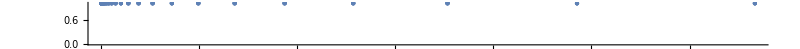
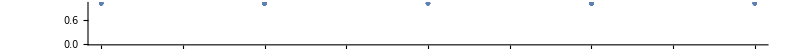
ρ: | -Graphics-
Ν: | -Graphics-

```mathematica
(*LoadFolder*)
SetDirectory[NotebookDirectory[]];
csvNames=FileNames["*.csv","./Data/"];
(*GetSortedCoordinates*)
csvCoords=Map[ToExpression,(StringSplit[#,{"/","_"}]&/@csvNames)[[All,3;;6]],Infinity];
ordering=Ordering[csvCoords];
csvCoords=csvCoords[[ordering]];
(*GetSortedIdentifiers*)
csvIdentifiers=(csvCoords//DeleteDuplicates);
(*GetSortedData*)
csvData=ParallelMap[Import[#]&,csvNames];
csvData=csvData[[ordering]];
(*GetSortedRepetitions*)
repetitionsIndexes=Flatten[Position[csvCoords,#]]&/@csvIdentifiers;
repetitionsData=(csvData[[#]]&/@repetitionsIndexes);
(*Statistics*)
{csvNames//Length,csvIdentifiers//Length}
rhoResolution=DeleteDuplicates[csvCoords[[All,1]]]//Length;
popResolution=DeleteDuplicates[csvCoords[[All,4]]]//Length;
rhoDensityPlot=NumberLinePlot[(csvIdentifiers/namingScalingFactor//N)[[All,1]],ImageSize->800];
popDensityPlot=NumberLinePlot[(csvIdentifiers/namingScalingFactor//N)[[All,4]],ImageSize->800];
densities=Grid[{
{"ρ:",rhoDensityPlot},
{"Ν:",popDensityPlot}
}]
```

```mathematica
Export["sampledDensitiesGrid.eps",densities]
```

sampledDensitiesGrid.eps

```mathematica
popSizes=DeleteDuplicates[csvCoords[[All,4]]]/namingScalingFactor
Directory[]
```

{10000,20000,30000,40000,50000}

/Users/chipdelmal/Dropbox/Final02/Experiment06/1Pop

```mathematica
Length/@repetitionsIndexes
%//Total
rhoResolution
```

{100,51,100,100,100,100,75,100,100,100,100,75,100,100,100,100,75,100,100,100,100,75,100,100,100,100,75,100,100,100,100,78,100,100,100,100,91,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,99,100,100,100,100,75,100,100,100,100,75,100,100,100,100,75,100,100,100,100,75,100,100,100,100,75,100,100,100,100,75,100,100,100,100,75,100,100,100,100,75,100,100,100,100,75,100}

15069

31

## Elimination Probabilities

### Probabilities Calculation

```mathematica
indexOfInterest=3;
(*------------------*)
eliminationBoolRepetitions=Table[
(**)
initPops=First/@repetitionsData[[i]][[All,indexOfInterest]];
lastPops=Last/@repetitionsData[[i]][[All,indexOfInterest]];
(**)
eliminationBool=If[#==0,1,0]&/@(lastPops)//N
,{i,1,repetitionsData//Length}];
(*------------------*)
meanEliminationProbabilities=Mean/@eliminationBoolRepetitions;
(*------------------*)
dataTuples={csvIdentifiers,meanEliminationProbabilities}//Transpose;
dataPointsFlat=Flatten/@({#[[1]]/namingScalingFactor,#[[2]]}&/@dataTuples//N);
```

### Raw Data Curves

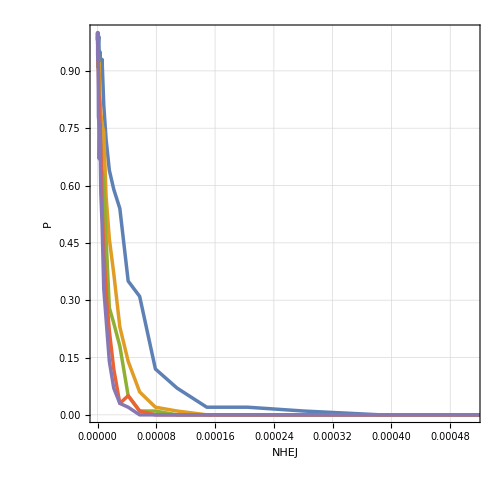
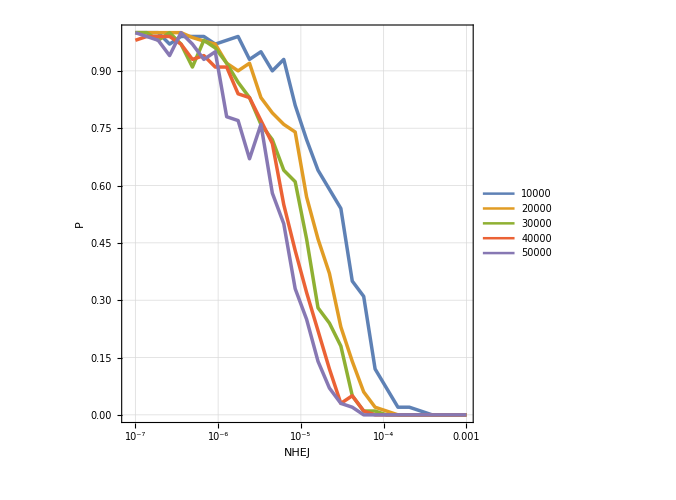
-Graphics- | -Graphics-

```mathematica
(*Getting Dataset*)
indVectors=dataTuples[[All,1,4]]//DeleteDuplicates;
data=Table[
dataset=Cases[dataTuples,{{rho_,Floor[.99*namingScalingFactor],0,indVectors[[i]]},out_}->N[{rho/namingScalingFactor,out}]]
,{i,1,indVectors//Length}];
(*Lin and Log data plots*)
crashProbLinLinData=ListPlot[data
(*,PlotLegends->(indVectors/namingScalingFactor)*)
,PlotStyle->Thickness[.005]
,Frame->frame
,Joined->True
,FrameTicksStyle->frameTicksStyle
,FrameLabel->{"NHEJ","P"}
,BaseStyle->baseStyle
,GridLines->Automatic
,FrameStyle->frameStyle
,GridLinesStyle->gridLinesStyle
,ImageSize->imageSize
,AspectRatio->aspectRatio
];
crashProbLogLinData=ListLogLinearPlot[data
,PlotLegends->(indVectors/namingScalingFactor)
,PlotStyle->Thickness[.005]
,Frame->frame
,Joined->True
,FrameTicksStyle->frameTicksStyle
,FrameLabel->{"NHEJ","P"}
,BaseStyle->baseStyle
,GridLines->Automatic
,FrameStyle->frameStyle
,GridLinesStyle->gridLinesStyle
,ImageSize->imageSize
,AspectRatio->aspectRatio
];
(*Grid*)
Grid[{{crashProbLinLinData,crashProbLogLinData}}]
```

### Elimination Curves Fits

#### Log

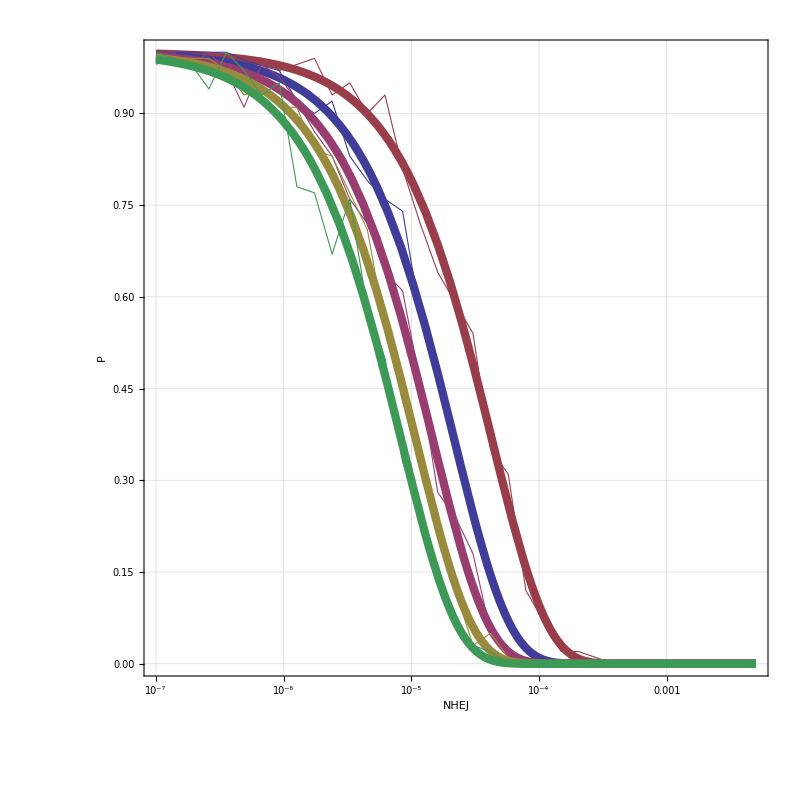
-Graphics- |

NHEJLog.png

```mathematica
(*Fit Data to Prototype Function*)
prototypeFunction[x_,k_,c_]:=ⅇ^(-k*x)
fits=Table[
nlm=NonlinearModelFit[data[[i]],prototypeFunction[x,k,c],{k,c},x];
{
Show[
LogLinearPlot[
nlm[x]
,{x,.0000001,.005}
,PlotStyle->{{Thickness[.0075],colors[[i]]}}
,PlotRange->{0,1}
],
ListLogLinearPlot[data[[i]],PlotStyle->{{Opacity[1],Thickness[.001],PointSize[.01],colors[[i]]}},Joined->True]
,Frame->True
,FrameTicksStyle->baseStyle
,FrameLabel->{"NHEJ","P"}
,BaseStyle->baseStyle
,GridLines->Automatic
,FrameStyle->Directive[Gray,Thick]
,GridLinesStyle->Directive[Gray,Thin,Dashed]
,ImageSize->imageSize
,AspectRatio->1
,PlotRange->{0,1}
]
,nlm//Normal
,nlm
}
,{i,1,data//Length}];
popLogFitsNormal=fits[[All,2]];
(*legends=StringJoin@@@Transpose[{ToString/@(indVectors/namingScalingFactor),ConstantArray[" :: [",Length[indVectors]],ToString/@StandardForm/@popLogFitsNormal,ConstantArray["]",Length[indVectors/namingScalingFactor]]}]*)
legends=ToString/@(indVectors/namingScalingFactor);
logFits=Grid[{{
fits[[All,1]]//Show[#,ImageSize->800,PlotLegends->Automatic]&,
LineLegend[colors,legends,LegendLabel->"N",LabelStyle->Directive[Thick,Gray,20]](*LineLegend[colors,legends,LegendLabel->"N :: [Exponential Decay]",LabelStyle->Directive[Thick,Gray,20]]*)
}}]
Export["NHEJLog.png",logFits,ImagePadding->50]
```

#### Lin

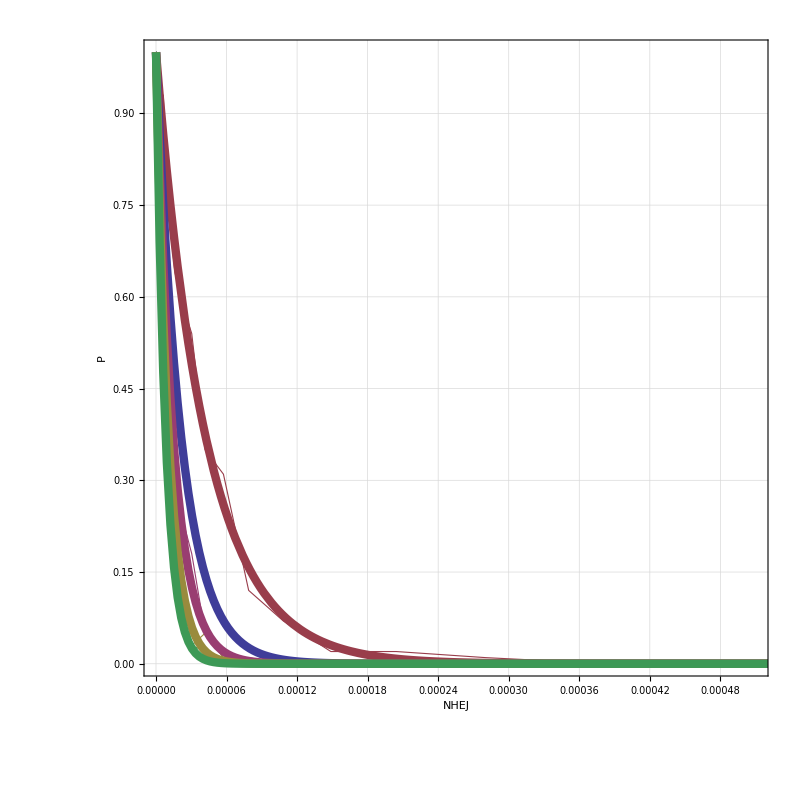

NHEJLinear.eps

```mathematica
functions=fits[[All,2]];
listLineProbabilitiesPlots=ListPlot[data
,PlotStyle->Table[{Thickness[thicknessLow],i},{i,colors}]
,Frame->frame
,Joined->True
,FrameTicksStyle->frameTicksStyle
,FrameLabel->{"NHEJ","P"}
,BaseStyle->baseStyle
,GridLines->Automatic
,FrameStyle->frameStyle
,GridLinesStyle->gridLinesStyle
,ImageSize->800
,AspectRatio->aspectRatio
];
fitProbabilitiesPlots=Table[
Plot[functions[[i]],{x,0,.01}
,PlotRange->{0,1}
,PlotStyle->{Thickness[thicknessHigh],colors[[i]]}
,PlotRange->{-1,1}
],{i,1,data//Length}]//Show[#]&;
linFits=Show[Flatten[{listLineProbabilitiesPlots,fitProbabilitiesPlots}]]
Export["NHEJLinear.eps",linFits,ImageSize->1000]
(*functions=fits[[All,2]];
fitsPlot=Plot[functions,{x,0,.001},PlotRange->{0,1},PlotLegends->Automatic,PlotStyle->{Thickness[thicknessHigh],colors}];
fitsAndPoints=Show[{listLineProbabilitiesPlots,fitsPlot}]*)
```

### Grid

```mathematica
Grid[{{linFits,logFits}}]
```

-Graphics- | -Graphics- |

### Breaking Points Calculations

#### Linear

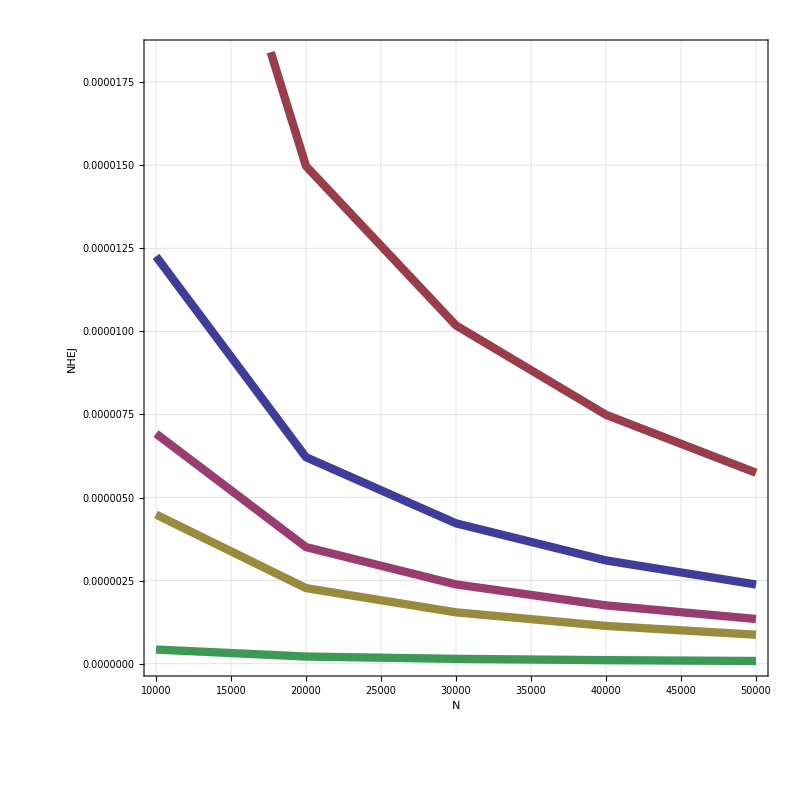

NHEJCriticalLinear.eps

```mathematica
confidence={.5,.75,.85,.9,.99};
breakingPoints=Table[Solve[fits[[All,2]][[i]]==#,x][[1,1,2]]//Quiet,{i,1,Length[fits]}]&/@confidence;
popCoords=Transpose[{popSizes,#}]&/@breakingPoints;
popSizeRho=ListLinePlot[popCoords
,PlotStyle->Table[{Thickness[thicknessHigh],i},{i,colors}]
,Frame->frame
,Joined->True
,InterpolationOrder->1
,FrameTicksStyle->frameTicksStyle
,FrameLabel->{"N","NHEJ"}
,BaseStyle->baseStyle
,GridLines->Automatic
,FrameStyle->frameStyle
,GridLinesStyle->gridLinesStyle
,ImageSize->800
,AspectRatio->aspectRatio]
Export["NHEJCriticalLinear.eps",popSizeRho,ImageSize->1000]
```

#### Inverse

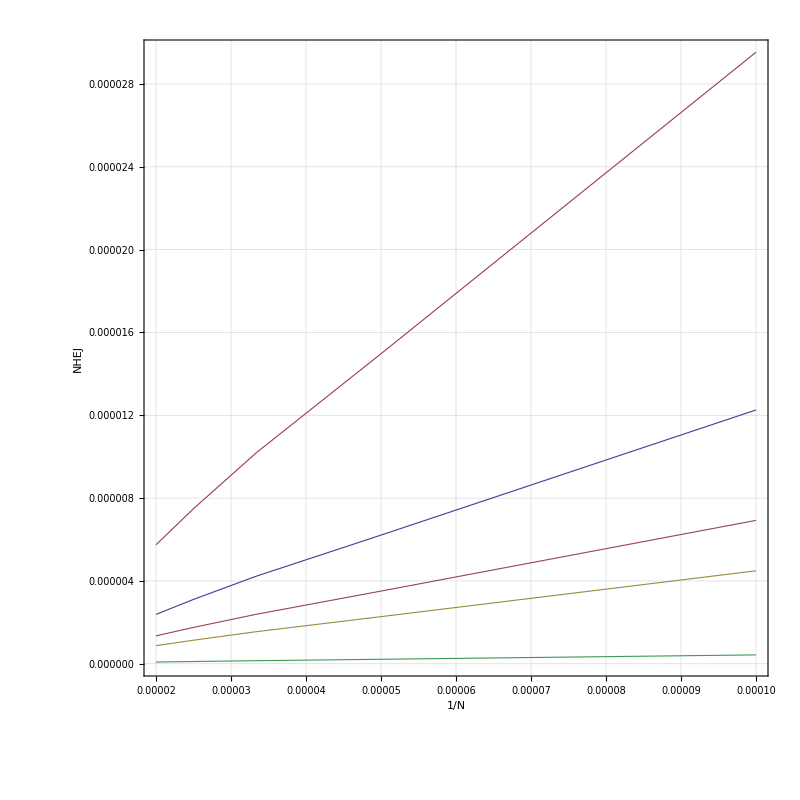
-Graphics- |

```mathematica
breakingPoints=Table[Solve[fits[[All,2]][[i]]==#,x][[1,1,2]]//Quiet,{i,1,Length[fits]}]&/@confidence;
popCoords=Transpose[{1/popSizes,#}]&/@breakingPoints;
popSizeRhoInv=ListLinePlot[popCoords
,PlotStyle->Table[{Thickness[thicknessLow],i},{i,colors}]
,Frame->frame
,Joined->True
,InterpolationOrder->1
,FrameTicksStyle->frameTicksStyle
,FrameLabel->{"1/N","NHEJ"}
,BaseStyle->baseStyle
,GridLines->Automatic
,FrameStyle->frameStyle
,GridLinesStyle->gridLinesStyle
,ImageSize->800
,AspectRatio->aspectRatio
,PlotRange->All
];
popSizeRhoInvLeg=Grid[{{
popSizeRhoInv,
LineLegend[colors,confidence,LegendLabel->"Crash Confidence",LabelStyle->Directive[Thick,Gray,20]]
}}]
```

#### Linear (Inverse) Fits

{0.296755 x,0.123164 x,0.0695786 x,0.0451076 x,0.00430281 x}

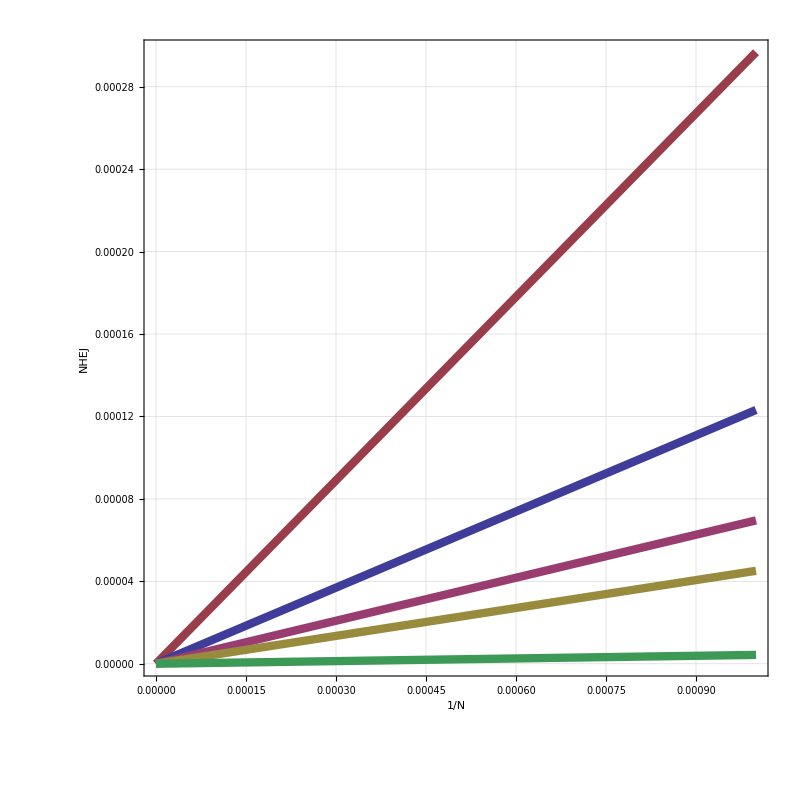

```mathematica
popLinearFits=NonlinearModelFit[#,m*x,{m,c},x]&/@popCoords;
popLinearFitsNormal=Normal/@popLinearFits
fitProbabilitiesPlots=Table[
Plot[
popLinearFits[[i]]//Normal
(*Callout[popLinearFits[[i]]//Normal,StringReplace[ToString[popLinearFitsNormal[[i]]],"x"->"1/N"],Top,LabelStyle->Directive[12.5,Gray],LeaderSize->10,Appearance->"None",CalloutMarker->"CirclePoint",Background->Directive[White,Opacity[0]]]*)
,{x,0,.001}
,PlotStyle->{Thickness[thicknessHigh],colors[[i]]}
,Frame->frame
,FrameTicksStyle->baseStyle
,FrameLabel->{"1/N","NHEJ"}
,BaseStyle->baseStyle
,GridLines->Automatic
,FrameStyle->frameStyle
,GridLinesStyle->gridLinesStyle
,ImageSize->800
,AspectRatio->aspectRatio
],{i,1,popLinearFits//Length}]//Show
(*legends=StringJoin@@@Transpose[{ToString/@confidence,ConstantArray[" :: [",Length[confidence]],ToString/@StandardForm/@popLinearFitsNormal,ConstantArray["]",Length[confidence]]}]*)
legends=ToString/@confidence;
```

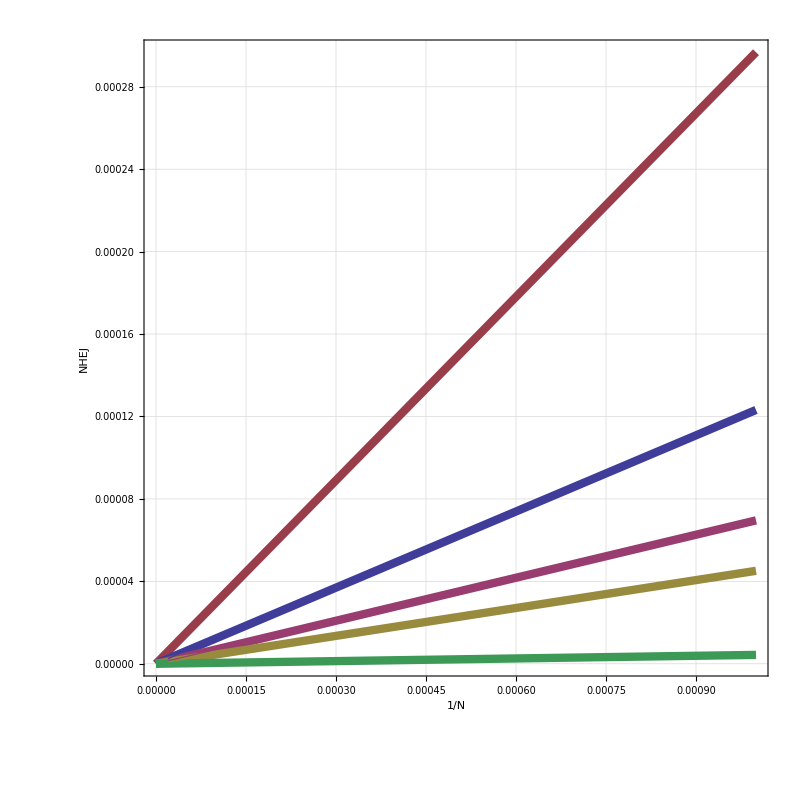
-Graphics- |

NHEJCriticalLog.png

```mathematica
linearFitsPlots=Grid[{{
Show[fitProbabilitiesPlots,popSizeRhoInv,ImagePadding->All],
LineLegend[colors,legends,LegendLabel->"Crash Confidence",LabelStyle->Directive[Thick,Gray,20]]
(*LineLegend[colors,legends,LegendLabel->"Crash Confidence :: [Linear Regression]",LabelStyle->Directive[Thick,Gray,20]]}*)
}}]
Export["NHEJCriticalLog.png",linearFitsPlots,ImagePadding->50]
```

### Full Grid

```mathematica
fullGrid=Grid[{
{linFits,logFits},
{popSizeRho,linearFitsPlots}
}
,Frame->{None,{True,True}}
,FrameStyle->Directive[Thick,Gray,Dashed]
]
Export["grid.tiff",fullGrid]
```

-Graphics- | -Graphics- | 
-Graphics- | -Graphics- |

grid.tiff